# 日本各大高校欧派函数对抗大赛选手权TOP10

欢迎访问http://nyuls.com/
以下函数整理自：https://weibo.com/1742250074/GtrzzrRX5
这个Notebook包含作者的评论、函数的绘图以及函数的LaTeX代码。

## No.1 埼玉大学（理学部）

作者のコメント：おーぱい好きや。正規分布に見せかけた乳首項と等角螺旋の組合せ。

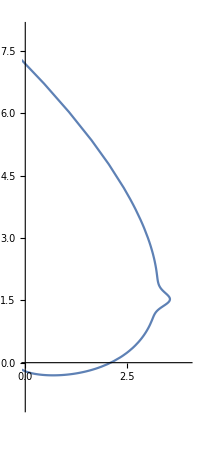

```mathematica
Clear["Global`*"];
ParametricPlot[{a Exp[c θ]Cos[c θ]+1/(p √(2π m^2))Exp[-(θ-n)^2/(2 m^2)],b Exp[b θ]Sin[d θ]}/.{a->2.09,b->1.31,c->1.16,d->0.885,m-> 0.036,n-> 0.615,p-> 35.237},{θ,-π/2,π/2},AspectRatio->Automatic,PlotRange->{{0,4},{-1,8}}]
```

```mathematica
\begin{cases}
x=a\mathrm e^{c \theta}\cos c\theta+\dfrac{\mathrm e^ {-\frac{(\theta -n)^2}{2 m^2}}}{\sqrt{2 \pi  m^2} p}\\
y=b\mathrm e^{b \theta}\sin d\theta
\end{cases}
a=2.09, b=1.31, c=1.16, d=0.885, m=0.036, n=0.615, p=35.237
```

## No.2 明治大学

作者のコメント：Bの美乳が好きです。

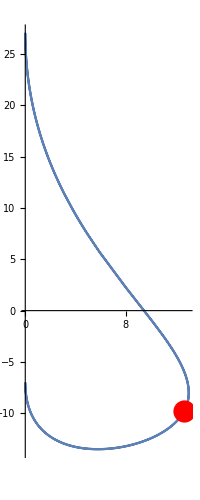

```mathematica
Show[ParametricPlot[#,{t,0,2Pi}],Graphics[{Red,PointSize[0.04],Point[#/.t->1.45]}]]&[{13 Sin[t]^4,-17Cos[t]+9Cos[2t]-1/10 Cos[3t]+Cos[4t]+1/10 Cos[5t]}]
```

```mathematica
\begin{cases}
x=13\sin^4t\\
y=-17\cos t+9\cos2t-\dfrac1{10}\cos3t+\cos4t+\dfrac1{10}\cos5t
\end{cases},
0\leqslant t\leqslant2\pi
```

## No.3 広島大学（理学部）

作者のコメント：Dカップお椀型こだわりは媒介変数を用いないと表せないおっぱい下部のたるみです。少しデコルテが歪んでしまったのが心残りです。

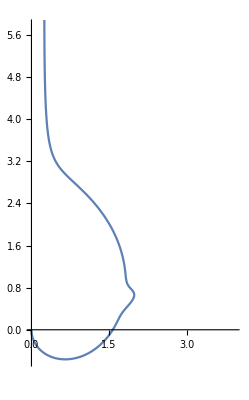

```mathematica
ParametricPlot[{(θ+π/2+0.005/(θ-π/2)^2+0.2Exp[-110(θ-0.1π)^2])Cos[θ],(θ+π/2+0.005/(θ-π/2)^2+0.2Exp[-110(θ-0.1π)^2])Sin[θ]},{θ,-Pi/2,Pi/2}]
```

```mathematica
\begin{cases}
x=\left(\dfrac{0.005}{\left(\theta -\pi/2\right)^2}+\mathrm e^{-110 (\theta -0.1 \pi )^2}+\theta +\dfrac{\pi }{2}\right) \cos\theta\\
y=\left(\dfrac{0.005}{\left(\theta -\pi/2\right)^2}+\mathrm e^{-110 (\theta -0.1 \pi )^2}+\theta +\dfrac{\pi }{2}\right) \sin\theta
\end{cases},
-\dfrac\pi2\leqslant\theta\leqslant\dfrac\pi2.
```

## No.4 東京農業大学

作者のコメント：おっぱいの成長過程を、一つの可変定数pを変化させることで表現しました。任意の時刻で静止することで、お好みのおっぱいを楽しむことができます。

作者的评论：我通过改变一个变量常数p表达了胸部的成长过程。 您可以随时停下来享受您最喜爱的胸部。

```mathematica
Π[x_,p_]:=(p(1-p/(π^2(1+π)))^2 x^2)/Exp[(1-p/π^π)x]+p^2/π^2 Sin[p/π^2(x+p/π^π)]/Exp[x]+(p^(1/π)/(2 π^2)+1/π^3)Exp[-π^(π^2-p/2)(x-p/(2 π^2)-2)^4]+(π-√p)/π^π Exp[-π^2(π-1)(x-p/(2 π^2)-2)^2]+p/π^4 Exp[-(π^2/p(x-p/(2 π^2)-2))^2];
Manipulate[Plot[Π[x,p],{x,0,6},AspectRatio->Automatic],{{p,3},1,4}]
```

```mathematica
y=&\frac{p \left(1-p/\left(\pi ^2 (1+\pi )\right)\right)^2 x^2}{\exp \left(\left(1-p/{\pi ^{\pi }}\right) x\right)}+{\frac{p^2 \sin \left(p \left(p/{\pi ^{\pi }}+x\right)/\pi ^2\right)}{\pi ^2 \exp (x)}}\\
&+\left(\frac{p^{1/\pi }}{2 \pi ^2}+\frac{1}{\pi ^3}\right) \exp \left(-\pi ^{\pi ^2-\frac{p}{2}} \left(-\frac{p}{2 \pi ^2}+x-2\right)^4\right)\\
&+\frac{\left(\pi -\sqrt{p}\right) }{\pi^\pi}\exp \left(-\pi ^2 (\pi -1) \left(-\frac{p}{2 \pi ^2}+x-2\right)^2\right)\\
&+\frac{p}{\pi ^4}\exp\left(-\left(\frac{\pi^2 \left(-p/(2\pi^2)+x-2\right)}{p}\right)^2\right)
```

## No.5 文教大学

作者のコメント：私の大学は先生になる人が全国的に見ても多い大学です。この関数によって性に目覚め始めた小中学生がより良いおっぱい人生を歩めるよう教えたいです。ちなみに私は小さい胸を気にしている娘をいじめるのが好きです。

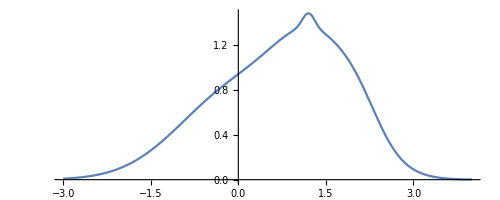

```mathematica
Plot[0.8Exp[-x^2/2]+Exp[-(x-1.4)^2]+1/6Exp[-(2x-4.17)^2]+1/8Exp[-(6.9x-8.3)^2],{x,-3,4},AspectRatio->Automatic]
```

```mathematica
y=\frac45\mathrm e^{-\frac{x^2}{2}}+\frac{1}{8}\mathrm e^{-(6.9 x-8.3)^2}+\frac{1}{6}\mathrm e^{-(2 x-4.17)^2}+\mathrm e^{-(x-1.4)^2}
```

## No.6 京都大学

作者のコメント：ガ乳勢の力を見せます。

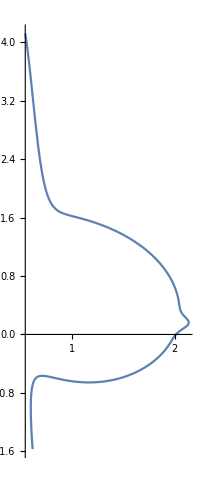

```mathematica
b=Log[GoldenRatio]/(π/2);
a=ArcTan[(-1+√(1+b^2))/b];
ParametricPlot[{Exp[b θ]Cos[θ]+1+1/π^2 Exp[-π^4(θ-a)^2],Exp[b θ]Sin[θ]-π LogisticSigmoid[-π (θ+π)]+π LogisticSigmoid[π^3(θ-1.793)]},{θ,-π,7π/12},AspectRatio->Automatic]
```

```mathematica
\varphi=\frac{\sqrt5-1}{2},b=\frac{\ln\varphi}{\pi/2},a=\arctan\frac{-1+\sqrt{1+b^2}}{b}\]
\begin{cases}
x=\dfrac1{\pi^2}\mathrm e^{-\pi ^4 (\theta -a)^2}+\cos\theta\mathrm e^{b\theta}+1\\
y=\mathrm e^{b\theta}\sin\theta+\dfrac{\pi}{1+\mathrm e^{-\pi^3 (\theta -1.793)}}-\dfrac{\pi}{1+\mathrm e^{\pi(\theta+\pi)}}
\end{cases},
-\pi\leqslant\theta\leqslant\dfrac{7}{12}\pi
```

## No.7 首都大学東京（積分サークル）

作者のコメント：y>0の範囲がおっぱいですが、おっぱいは女の子についてこそ美しいのでその周囲も関数で表現しました。点(-4,0)近傍の鎖骨がポイントです。

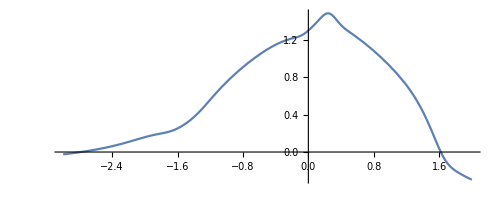

```mathematica
Plot[1.2Exp[-0.5 x^2]+Exp[0.1x]-1.3^(0.6x)-1.1^-x+0.2Exp[-7(x-0.8)^8]+0.1Exp[-(8x-2)^2]-1.1^(x-6)+0.4Exp[-0.04 x^8]+0.4Exp[-0.04(x+3)^8]+1.2,{x,-3,2},AspectRatio->Automatic]
```

```mathematica
\begin{align*}
y=&0.4\mathrm e^{-0.04 x^8}+1.2\mathrm e^{-0.5 x^2}+0.1\mathrm e^{-(8 x-2)^2}+0.2\mathrm e^{-7 (x-0.8)^8}\\
&+0.4\mathrm e^{-0.04 (x+3)^8}+\mathrm e^{0.1 x}-1.1^{x-6}-1.1^{-x}-1.3^{0.6 x}+1.2
\end{align*}
```

## No.8 航空保安大学校

这个表达式实在是丧心病狂，就先不抄了。

## No .9 大阪大学

作者のコメント：今回は優秀な曲線美をもつ √(xⅇ^(-x^2))を元に関数を作成しました。この関数の特徴は単位おっぱい関数，即ち主要部が縦横ともに±1を基準に存在している点です。この関数で入賞することを祈ります。

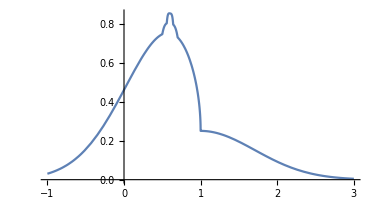

```mathematica
Plot[(√((Abs[1-x]+1-x)/2)+1/4)Exp[-(1-x)^2]+1/40(Abs[1-2^4(5x-3)^4]+Abs[1-2^9(5x-3)^4]+2-528(5x-3)^4),{x,-1,3},AspectRatio->Automatic]
```

```mathematica
\begin{align*}
y=&\left(\sqrt{\frac{|1-x|-x+1}{2}}+\frac{1}{4}\right)\mathrm e^{-(1-x)^2}\\
&+\frac{1}{40} \left(\left| 1-2^4 (5 x-3)^4\right| +\left|1-2^9 (5 x-3)^4\right| -528 (5 x-3)^4+2\right)
\end{align*}
```

## No.10 名古屋大学

作者のコメント：揺れない乳は乳と呼べません。tを変数とする正弦関数を式中に含ませることで，滑らかな揺れを再現しました。単に平行移動するのではな弾力のある乳がしなやかに動く様子をお楽しみいただけることでしょう。

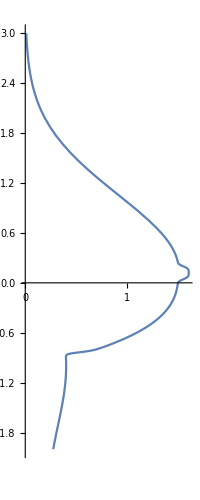

```mathematica
ParametricPlot[{(1.5Exp[-0.62(y-0.16)^2])/(1+Exp[-20(5y-1)])+((1.5+0.8(y-0.2)^3)(1+Exp[20(5y-1)])^-1)/(1+Exp[-(100(y+1)-16)])+(0.2(Exp[-(y+1)^2]+1))/(1+Exp[100(y+1)-16])+0.1/Exp[2(10y-1.2)^4],y},{y,-2,3}]
```

```mathematica
x=\frac{0.2 \left(\mathrm e^{-(y+1)^2}+1\right)}{\mathrm e^{100 (y+1)-16}+1}+\frac{1.5\mathrm e^{-0.62 (y-0.16)^2}}{\mathrm e^{-20 (5 y-1)}+1}+\frac{0.1}{\mathrm e^{2 (10 y-1.2)^4}}+\frac{0.8 (y-0.2)^3+1.5}{(\mathrm e^{-(100 (y+1)-16)}+1)(\mathrm e^{20 (5 y-1)}+1)}
```